```mathematica
<<peeters`

(*relative to ~/physicsplay*)
peeters`setGitDir[ "../project/figures/blogit" ]
```

peeters`

/Users/pjoot/project/figures/blogit

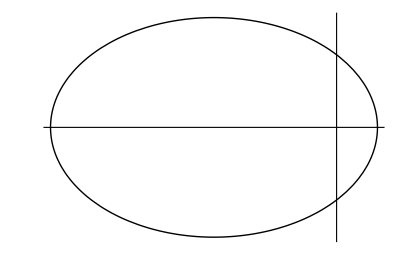

```mathematica
ClearAll[t, p, ellipseFig1, f, a, c]

f[e_, d_, t_] := {Cos[t], Sin[t]}e d/( 1 + e Cos[t])
a[e_, d_] := e d/(1 - e^2);
c [e_, d_] = a[e,d] e;
p[e_, d_] := ParametricPlot[f[e,d,t], {t, 0, 2 Pi}, PlotStyle-> {Thick, Black},
Ticks -> None,
PlotRange-> All
]

Manipulate[p[e,d],
{{e, 0.75},0,1},
{{d, 1},0,10}]

ellipseFig1 = p[0.75, 1]
```

```mathematica
peeters`exportForLatex["ellipseFig1",ellipseFig1]
```

{ellipseFig1.eps,ellipseFig1pn.png}

```mathematica
ClearAll[animation, orbit]

(* a,b,c,e: conventions from Salus/Hille, 9.4 conic sections. *)
animation[a_, c_] := Module[{ellipse,e, len, b},
b = Sqrt[a^2 - c^2];
ellipse[t_] := {a Cos[t], b Sin[t]};
e = c/a;
(*len[t_] := N[Norm[{c, 0} -ellipse[t]] + Norm[{-c, 0} -ellipse[t]]];*)

Animate[
Show[{
ParametricPlot[ellipse[t], {t, 0, 2 Pi}, PlotStyle-> {Thick, White},
Ticks -> None,
PlotRange-> 2{{-1,1},{-1,1}1080/1920},
Ticks -> None,
PlotStyle-> {White},
Background-> Black
],
Graphics[{
White,
PointSize -> Small,
Point[ {-c, 0} ],
Line[{{c, 0} ,ellipse[t]}],
Line[{{-c, 0} ,ellipse[t]}],
Blue//Darker,
PointSize[0.03],
Point[ ellipse[t] ],
PointSize[0.1],
Yellow//Darker,
Point[ {c, 0} ]
(*,
Text[ ToString[len[t]], {0,0}]*)
}]
},
ImageSize -> {1920, 1080 }],
{t, 0, 6 Pi},
AnimationDirection->Forward,
AnimationRate -> 0.3,
DisplayAllSteps->True,
DefaultDuration -> 20,
]
]

orbit = animation[1, 0.65];

Export["earthOrbiting.mp4", orbit]
```

earthOrbiting.mp4

```mathematica
ClearAll[t, deltaT, a, c, b, ellipse, t, duration, s1, e1]
duration = 4;
deltaT = 4 Pi/(duration * 100);
t = 0;
a = 1;
c = 0.65;

b = Sqrt[a^2 - c^2];
ellipse[t_] := {a Cos[t], b Sin[t]};
e = c/a;
s1 = Import["sun.jpeg", ImageSize->{200,200}];
e1 =  Import["earth.jpeg", ImageSize->{40,40}];
anim = Table[
Show[{
ParametricPlot[
ellipse[th], {th, 0, 2 Pi}, 
PlotStyle-> {Thick, White},
Ticks -> None,
PlotRange-> 2{{-1,1},{-1,1}1080/1920},
Ticks -> None,
PlotStyle-> {White},
Background-> Black
],
Graphics[{
White,
PointSize -> Small,
Point[ {-c, 0} ],
Line[{{c, 0} ,ellipse[t]}],
Line[{{-c, 0} ,ellipse[t]}],
Inset[e1, ellipse[t]],
(*Blue//Darker,
PointSize[0.03],
Point[ ellipse[t] ],*)
(*PointSize[0.1],*)
(*Yellow//Darker,
Point[ {c, 0} ]*)
Inset[s1, {c,0}]
}]
},
ImageSize -> {1920, 1080 }
],{t, 0, 4 Pi, deltaT}];
(*ListAnimate[anim]*)

Export["earthOrbiting.5.mp4", anim]
```

earthOrbiting.5.mp4

```mathematica
(*Export["earthOrbiting.mp4", anim]*)
```